Invasion Analysis for antagonistically specializing hosts. We begin with parameter definitions:

```mathematica
(* v = specialist 1 frequency, p = specialist 2 frequency, m = frequency mutant 1, n = frequency of mutant host 2, frequency Α = alpha, δ = alpha_g, s = specialist carbon proportion shared, g = generalist carbon proportion shared, u = symbiont 1 frequency *)
```

A generic tradeoff function which could be convex, concave or linear depending on the value of the constant, c. Host 1 mutants extract Α+d, while host 2 mutants extract Λ +z, causing f(Α) and f(Λ) to decrease accordingly.

```mathematica
(1-Α^(1-c))^c;
(1-(Α+d)^(1/c))^c;
(1-Λ^(1-c))^c;
(1-(Λ+z)^(1/c))^c;
```

Using these parameter definitions, we define the frequency of each strategist over time:

```mathematica
Clear["Global`*"]
System[Α_,Λ_,δ_, g_, s_,d_,z_,c_,m0_,n0_,u0_,v0_,p0_]:={u'[t]==-s (-1+u[t]) u[t] ((-d-Α+(1-(d+Α)^(1/c))^c) m[t]+(z+Λ-(1-(z+Λ)^(1/c))^c) n[t]+Λ p[t]-(1-Λ^(1/c))^c p[t]-Α v[t]+(1-Α^(1/c))^c v[t]),v'[t]==v[t] (-s (-s+(1-Α^(1/c))^c) (-1+u[t])+s (-s+Α) u[t]+s m[t] ((-s+(1-(d+Α)^(1/c))^c) (-1+u[t])-(d-s+Α) u[t])+s p[t] (s-Λ+(Λ-(1-Λ^(1/c))^c) u[t])+s n[t] (s-z-Λ+(z+Λ-(1-(z+Λ)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),p'[t]==p[t] (s (s-Λ) (-1+u[t])+s (-s+(1-Λ^(1/c))^c) u[t]+s m[t] ((-s+(1-(d+Α)^(1/c))^c) (-1+u[t])-(d-s+Α) u[t])+s p[t] (s-Λ+(Λ-(1-Λ^(1/c))^c) u[t])+s n[t] (s-z-Λ+(z+Λ-(1-(z+Λ)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),m'[t]==m[t] (-s (-s+(1-(d+Α)^(1/c))^c) (-1+u[t])+s (d-s+Α) u[t]+s m[t] ((-s+(1-(d+Α)^(1/c))^c) (-1+u[t])-(d-s+Α) u[t])+s p[t] (s-Λ+(Λ-(1-Λ^(1/c))^c) u[t])+s n[t] (s-z-Λ+(z+Λ-(1-(z+Λ)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),n'[t]==n[t] (s (-s+z+Λ) (1-u[t])+s (-s+(1-(z+Λ)^(1/c))^c) u[t]-m[t] (s (-s+(1-(d+Α)^(1/c))^c) (1-u[t])+s (d-s+Α) u[t])-p[t] (s (-s+Λ) (1-u[t])+s (-s+(1-Λ^(1/c))^c) u[t])-n[t] (s (-s+z+Λ) (1-u[t])+s (-s+(1-(z+Λ)^(1/c))^c) u[t])-g (-g+δ) (1-m[t]-n[t]-p[t]-v[t])-(s (-s+(1-Α^(1/c))^c) (1-u[t])+s (-s+Α) u[t]) v[t]),WhenEvent[{m[t]≤0,m[t]≥1},m'[t]->0],p[0]==p0-n0,u[0]==u0,v[0]==v0-m0,m[0]==m0,n[0]==n0}
```

We a0:

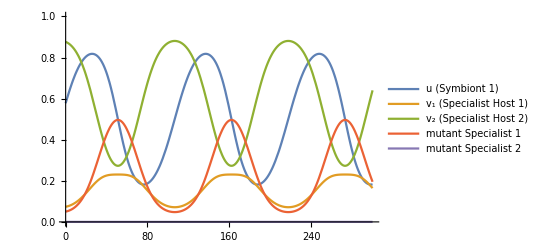

```mathematica
Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]:=System[0.6,0.6,0.3, 0.5, 0.5,d,z,c,m0,n0,u0,v0,p0];
{u0,v0,p0}={0.85,0.16,0.16};
      (*Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]*)
num=Simpl[0,0,1,0,0,u0,v0,p0];
Ans=NDSolve[num,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{u0, v0, p0, m0, n0} = {u[1200],v[1200],p[1200],m[1200],n[1200]}/. Flatten[Ans];
numl=Simpl[0.1,0,1,0.05,0,u0,v0,p0];
Ansl=NDSolve[numl,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Ansl];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

Any value is stable. We next consider the outcome of invasion when the tradeoff is convex (c=2) under similar initial conditions:

NDSolve::svnder: The variables {m'} in m'[t]→0 cannot be set as state variables while solving as an ODE because some are the highest order derivatives. You may be able to use these if you solve as a system of DAEs by using Method->{"EquationSimplification"->"Residual"}.

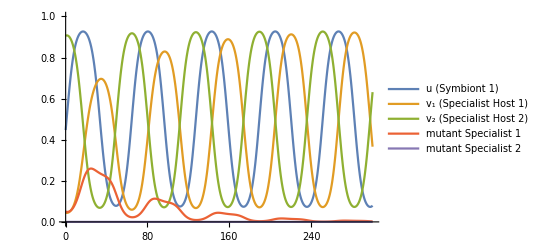

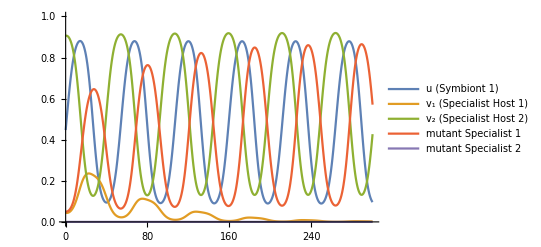

```mathematica
ClearAll[c,d,z,n0,v0,p0,v0,m0]
Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]:=System[0.6,0.6,0.3, 0.5, 0.5,d,z,c,m0,n0,u0,v0,p0];
{u0,v0,p0}={0.85,0.16,0.16};
        (*Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]*)
num=Simpl[0,0,2,0,0,u0,v0,p0];
Ans=NDSolve[num,{u,v,p,m,n},{t,0,3000}];
{u0, v0, p0, m0, n0} = {u[1200],v[1200],p[1200],m[1200],n[1200]}/. Flatten[Ans];
	       (*Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]*)
(*Here we consider an invading mutant with a reduced value of matched extraction *)
numcv=Simpl[-0.1,0,2,0.05,n0,u0,v0,p0];
Anscv=NDSolve[numcv,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Here we consider an invading mutant with an increased value of matched extraction *)
numcv=Simpl[0.1,0,2,0.05,n0,u0,v0,p0];
Anscv=NDSolve[numcv,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

We see that increased values of resource extraction are always able to supplant resident values of extraction. We also consider the impact of symmetric invasion of a mutant of the opposite type, after the host 1 mutant replaces specialist host 1.

{0.247028,0.107633,0.892367,0,0.}

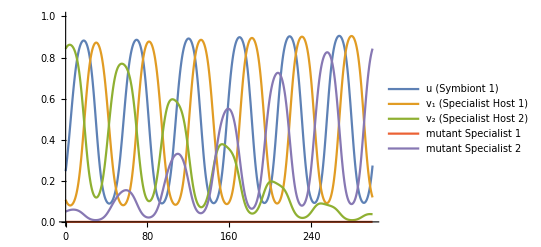

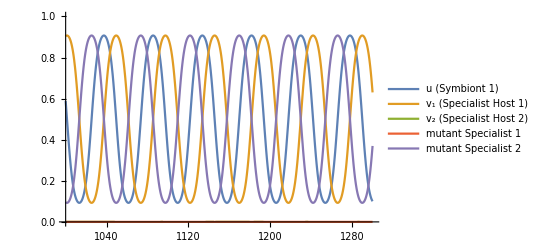

```mathematica
{u0, v0, p0, m0, n0} = {u[1200],m[1200],p[1200],0,n[1200]}/. Flatten[Anscv]  (*      System[Α_,  Λ_, δ_,  g_,  s_, d_,z,c,m0_ ,n0_, u0_,v0_,p0_]*)
numcv=  System[0.7,0.6,0.3, 0.5, 0.5,0,0.1,2,0,0.05,   u0,v0,p0];
Anscv2=NDSolve[numcv,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv2];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
Plot[{uans,vans,pans,mans,nans},{t,1000,1300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

Mutants with greater values of alpha always fix in the population. Finally, consider a concave tradeoff for alpha (c=1/2):

NDSolve::svnder: The variables {m'} in m'[t]→0 cannot be set as state variables while solving as an ODE because some are the highest order derivatives. You may be able to use these if you solve as a system of DAEs by using Method->{"EquationSimplification"->"Residual"}.

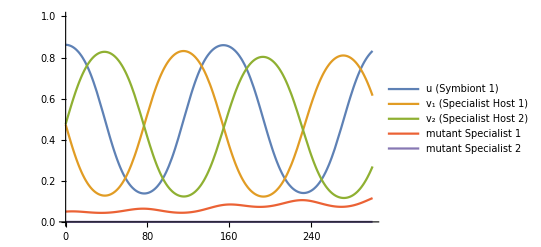

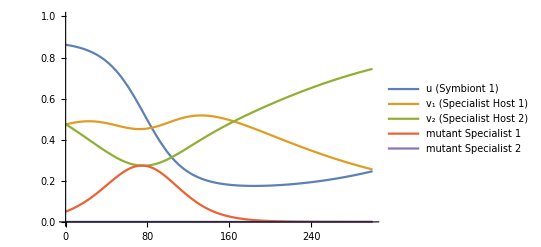

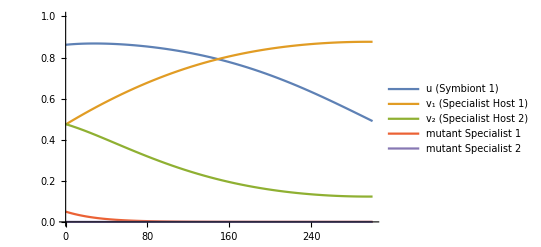

```mathematica
ClearAll[c,d,z,n0,v0,p0,v0,m0]
Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]:=System[0.6,0.6,0.3, 0.5, 0.5,d,z,c,m0,n0,u0,v0,p0];
{u0,v0,p0}={0.85,0.16,0.16};
        (*Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]*)
num=Simpl[0,0,0.5,0,0,u0,v0,p0];
Ans=NDSolve[num,{u,v,p,m,n},{t,0,3000}];
{u0, v0, p0, m0, n0} = {u[1200],v[1200],p[1200],m[1200],n[1200]}/. Flatten[Ans];
	       (*Simpl[d_,z_,c_,m0_,n0_,u0_,v0_,p0_]*)
(*There is an uninvadible value of alpha, first we consider the ability of mutants with this value of alpha to invade:  *)
numcv=Simpl[0.12,0,0.5,0.05,n0,u0,v0,p0];
Anscv=NDSolve[numcv,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(* Next, consider the ability of a mutant with an alternative value of alpha to invade: *)
numcv3=System[0.72,0.72,0.3, 0.5, 0.5,0.1,0,0.5,0.05,0,u0,v0,p0];
Anscv3=NDSolve[numcv3,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv3];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
numcv3=System[0.72,0.72,0.3, 0.5, 0.5,-0.1,0,0.5,0.05,0,u0,v0,p0];
Anscv3=NDSolve[numcv3,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Anscv3];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

Finally we consider the outcome of an invading host with an alternative value of proportion of resource trade allocation x. Host 1 allocated proportion s to trade and host 2 allocated proportion q to trade, removing the assumption of symmetry. Host 1 mutants receive (s+b) and host 2 mutants receive (q+f). We consider the change in frequency of all strategists, including host 1 and host 2 mutants:

```mathematica
Clear["Global`*"]
xmut[Α_,Λ_,δ_, g_, s_,q_,d_,z_,c_,b_,f_,m0_,n0_,u0_,v0_,p0_]:={u'[t]==(1-u[t]) u[t] ((b+s) (-d-Α+(1-(d+Α)^(1/c))^c) m[t]-(f+q) (-z-Α+(1-(z+Α)^(1/c))^c) n[t]-(-Α+(1-Α^(1/c))^c) (q p[t]-s v[t])),v'[t]==v[t] (-s (-s+(1-Α^(1/c))^c) (-1+u[t])+s (-s+Α) u[t]+q p[t] (q-Α+(Α-(1-Α^(1/c))^c) u[t])+(b+s) m[t] (b+s-(1-(d+Α)^(1/c))^c+(-d-Α+(1-(d+Α)^(1/c))^c) u[t])-n[t] (s (-f-q+z+Α)+(-s (z+Α)+(f+q) (1-(z+Α)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),p'[t]==p[t] (q (q-Α) (-1+u[t])+q (-q+(1-Α^(1/c))^c) u[t]+q p[t] (q-Α+(Α-(1-Α^(1/c))^c) u[t])+(b+s) m[t] (b+s-(1-(d+Α)^(1/c))^c+(-d-Α+(1-(d+Α)^(1/c))^c) u[t])-n[t] (s (-f-q+z+Α)+(-s (z+Α)+(f+q) (1-(z+Α)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),m'[t]==m[t] (-(b+s) (-b-s+(1-(d+Α)^(1/c))^c) (-1+u[t])+(b+s) (-b+d-s+Α) u[t]+q p[t] (q-Α+(Α-(1-Α^(1/c))^c) u[t])+(b+s) m[t] (b+s-(1-(d+Α)^(1/c))^c+(-d-Α+(1-(d+Α)^(1/c))^c) u[t])-n[t] (s (-f-q+z+Α)+(-s (z+Α)+(f+q) (1-(z+Α)^(1/c))^c) u[t])+s ((-s+(1-Α^(1/c))^c) (-1+u[t])+(s-Α) u[t]) v[t]-g (g-δ) (-1+m[t]+n[t]+p[t]+v[t])),n'[t]==n[t] (s (-f-q+z+Α) (1-u[t])+(f+q) (-s+(1-(z+Α)^(1/c))^c) u[t]-m[t] ((b+s) (-b-s+(1-(d+Α)^(1/c))^c) (1-u[t])+(b+s) (-b+d-s+Α) u[t])-p[t] (q (-q+Α) (1-u[t])+q (-q+(1-Α^(1/c))^c) u[t])-n[t] (s (-f-q+z+Α) (1-u[t])+(f+q) (-s+(1-(z+Α)^(1/c))^c) u[t])-g (-g+δ) (1-m[t]-n[t]-p[t]-v[t])-(s (-s+(1-Α^(1/c))^c) (1-u[t])+s (-s+Α) u[t]) v[t]),WhenEvent[{m[t]≤0,m[t]≥1},"StopIntegration"],p[0]==-n0+p0,u[0]==u0,v[0]==v0-m[0],m[0]==m0,n[0]==n0};
```

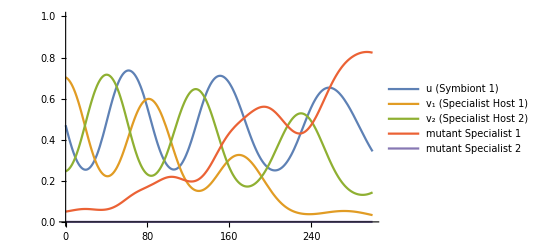

```mathematica
(*xmut[Α_,Λ_,δ_, g_, s_,q_,d_,z_,c_,b_,f_,m0_,n0_,u0_,v0_,p0_]*)
numx=xmut[0.6,0.6,0.3, 0.6, 0.6,0.6,0,0,2,0.1,0,0,0,0.7,0.15,0.17];
Ansx=NDSolve[numx,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{u0, v0, p0, m0, n0} = {u[1200],v[1200],p[1200],m[1200],n[1200]}/. Flatten[Ansx];
(* x = 1/4 (alpha+f(alpha)) is an optimal value of x that maximizes return on investment over a cycle period. Mutants with this value of x always successfully invade:  *)
	(*xmut[ Α_,  Λ_, δ_,  g_,  s_,  q_, d_,z_,c_,  b_, f_, m0_,n0_,u0_,v0_,p0_]*)
numxm=xmut[0.6,0.6,0.3, 0.7, 0.3,0.3,0,0,2,-0.18,0,0.05,0,u0,v0,p0];
Ansxm=NDSolve[numxm,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Ansxm];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

Once investment reached this stable equilibrium, alternative values of investment in the focal strategist type are unable to invade:

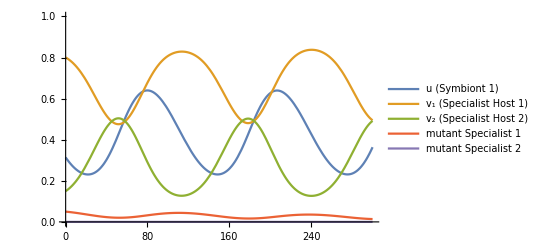

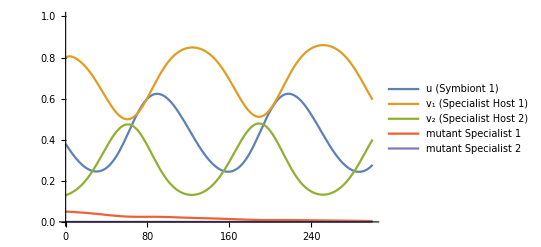

```mathematica
(*Consider first larger values of invading mutant alpha: *)
{u0, v0, p0, m0, n0} = {u[1200],m[1200],p[1200],0,0}/. Flatten[Ansxm];
numxm=xmut[0.6,0.6,0.3, 0.7, 0.12,0.3,0,0,2,+0.07,0,0.05,0,u0,v0,p0];
Ansxm=NDSolve[numxm,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Ansxm];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Consider next reduced values of invading mutant alpha: *)
{u0, v0, p0, m0, n0} = {u[500],v[500],p[500],0,0}/. Flatten[Ansxm];
numxm=xmut[0.6,0.6,0.3, 0.7, 0.12,0.3,0,0,2,-0.07,0,0.05,0,u0,v0,p0];
Ansxm=NDSolve[numxm,{u,v,p,m,n},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,vans,pans,mans,nans}= {u[t],v[t],p[t],m[t],n[t]} /.Flatten[Ansxm];
Plot[{uans,vans,pans,mans,nans},{t,0,300}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```